```mathematica
note[b_,x0_,t_,v_]:=Module[{a=b},Which[x0=="1",AppendTo[a,SoundNote[0,t,SoundVolume->v]],x0=="2",AppendTo[a,SoundNote[2,t,SoundVolume->v]],x0=="3",AppendTo[a,SoundNote[4,t,SoundVolume->v]],x0=="4",AppendTo[a,SoundNote[5,t,SoundVolume->v]],x0=="5",AppendTo[a,SoundNote[7,t,SoundVolume->v]],x0=="6",AppendTo[a,SoundNote[9,t,SoundVolume->v]],x0=="7",AppendTo[a,SoundNote[11,t,SoundVolume->v]],x0=="0",AppendTo[a,SoundNote[None,t,SoundVolume->v]],x0=="-",a[[-1,2]]+=t,x0=="_",a[[-1,2]]/=2,x0=="*",a[[-1,2]]*=1.5,x0=="t",a[[-1,2]]/=3,x0==".",a[[-1,1]]-=12,x0=="'",a[[-1,1]]+=12,x0=="#",a[[-1,1]]+=1,x0=="b",a[[-1,1]]-=1];a];
noteh[b_,x0_]:=Module[{h=b},Which[x0=="1",AppendTo[h,0],x0=="2",AppendTo[h,2],x0=="3",AppendTo[h,4],x0=="4",AppendTo[h,5],x0=="5",AppendTo[h,7],x0=="6",AppendTo[h,9],x0=="7",AppendTo[h,11],x0==".",h[[-1]]-=12,x0=="'",h[[-1]]+=12,x0=="#",h[[-1]]+=1,x0=="b",h[[-1]]-=1];h];

soundtrack[s_,t_,x_]:=Module[{lh=StringLength[x],xx=x,a={},v=1,par=False,h={},i,x0},For[i=1,i≤lh,i++,x0=StringTake[xx,1];
If[par,If[x0==")",AppendTo[a,SoundNote[h,t,SoundVolume->v]];par=False;
h={},h=noteh[h,x0]],If[x0=="(",par=True,v=Which[x0=="p",0.5,x0=="P",0.2,x0=="M",0.65,x0=="m",0.8,x0=="f",1,True,v];a=note[a,x0,t,v]]];
xx=StringDrop[xx,1]];
Sound[Prepend[a,s],{0,Plus@@(#[[2]]&/@a)}]];
```

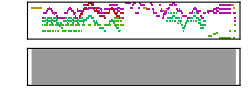

```mathematica
Shangaoshuichang=Sound[{soundtrack["Violin",0.5,
"00000000|0000000000000000|0000000000000000|p(3'5')---(4'6')---(2'4')---(61')3'_2'_1'6|(1'3')---(3'5')---m(1'3'5')-(62'4')-p(51'3')--0|P6'-6'-4'*5'_6'-1'1'4'6'_5'_5'--0|3'-3'6'5'3'_2'_1'-665'2'_3'_2'_m5_6_7_1'_7_1'_2'_|f3'4'5'*5'_6'6'_6'_5'5'_3'_2'2'_3'_2'1'6'.--0|51'1'*2'_3'3'_4'_3'2'_1'_2'2'6_5*1'-0m2'_1'_|2'2'--(1'3')-(2'4')-(1'3'5')-------|(1'3'5')001'_1'_(1351')00000000000|"],
soundtrack["Guitar",0.5,
"p00000000|1_(35)(35)_5._(35)_1_(24)_1_(35)(35)_5._(35)_1_(24)_|1_(35)(35)_5._(35)_1_(24)_1_2_1_7._1_2_6._5._|1_(35)(35)_5._(35)_1_(24)_1_(35)(35)_5._(35)_1_(24)_|1_(35)(35)_5._(35)_1_(24)_1_(35)(35)_5._(35)_1_(24)_|345*5_66_6_55_3_22_3_216.--0|5.11*2_33_4_321_7._1_6._6.5.1--0|0000000000000000|0000000000000000|M3_5_1'_5_3_5_1'_5_3_6_1'_6_3_5_1'_5_|2_3_5_3_2_3_5_1_6._5._6._7._1_2_3_4_|3_5_1'_5_3_5_1'_5_3_6_1'_6_3_5_1'_5_m(24)-(16.)-(13)-0m2'_1'_|2'2'--3'-4'-5'-------|5'001'_1'_1'00000000000|"],
soundtrack["Whistle",0.5,
"00000000|51'1'*2'_3'3'_4'_3'2'1'*7'._1'6'.5'.--0|5'.1'1'*2'_3'3'_4'_3'2'1'_7'._1'_6'._5'.3'_2'_2'--0|0000000000000000|0000000000000000|0000000000000000|0000000000000000|0000000000000000|0000000000000002'_1'_|2'2'--3'-4'-5'-------|5'001'_1'_1'00000000000|"],
soundtrack["Xylophone",0.5,"00000000|0000000000000000|0000000000000000|0000000000000000|0000000000000000|6'-6'-4'*5'_6'-1'1'4'6'_5'_5'--0|3'-3'6'5'3'_2'_1'-665'2'_3'_2'--0|0000000000000000|0000000000000002'_1'_|2'2'--3'-4'-5'-------|5'--1'_1'_1'00000000000|"],
soundtrack["Flute",0.5,
"00000000|0000000000000000|0000000000000_5_6_7_1'_7_1'_2'_|3'4'5'*5'_6'6'_6'_5'5'_3'_2'2'_3'_2'1'6'.--0|5'.1'1'*2'_3'3'_4'_3'2'1'_7'._1'_6'._6'.5'.1'--0|0000000000000000|0000000000000000|0000000000000000|0000000000000002'_1'_|2'2'--3'-4'-5'-------|5'001'_1'_1'00000000000|"],
soundtrack["SynthDrum",0.5,
"00000000|P5.0115.0115.0115.011|5.0115.0115.0115.000|P1000100010001000|10001000(135)0(135)0(135)010|0000000000000000|0000000000000000|0000000000000000|0000000000000000|f2.2.003.04.01.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__1.__|(5.1.)001.__1.__1.__1.__(5.1)00000000000|"],
soundtrack["Bird",0.5,
"p4'-4'-4'-4'-|0000000000000000|0000000000000000|0000000000000000|0000000000000000|00000000000000P4'4'|000000000000000|0000000000000000|0000000000000000|0000000000000000|00004'00000000000|"]}]
```

```mathematica
Export["山高水长Mathematica版.mp3",Shangaoshuichang]
```

Export::chtype: First argument Sound[{«1»}] is not a valid file specification.